# Genetic Evolution of Wolfram Models

The idea is to use genetic evolution to modify rules for a Wolfram Model to satisfy an objective. This means starting from a rule and performing mutation and crossover on individual replacements to build up a more complex rule. The population can be managed based on any kind of objective function.

## Initial Tests

```mathematica
wm=ResourceFunction["WolframModel"];
plot=ResourceFunction["WolframModelPlot"];
```

```mathematica
(* random initial rule *)
signature = {{2,2}}->{{3,2}};
rule = ResourceFunction["RandomWolframModel"][signature]
```

{{1,2},{2,3}}→{{2,4},{4,1},{1,3}}

```mathematica
steps=10;
init={{1,1},{1,1}};
```

```mathematica
final=wm[rule, init, steps, "FinalState"]
```

{{36,10},{20,3},{46,8},{32,47},{47,22},{22,15},{33,48},{48,23},{23,1},{34,49},{49,16},{16,14},{14,50},{50,1},{1,5},{35,51},{51,24},{24,5},{7,52},{52,5},{5,36},{10,53},{53,15},{15,11},{37,54},{54,25},{25,17},{38,55},{55,26},{26,18},{12,56},{56,18},{18,8},{39,57},{57,27},{27,19},{40,58},{58,28},{28,20},{41,59},{59,6},{6,3},{29,60},{60,3},{3,9},{42,61},{61,9},{9,13},{13,62},{62,19},{19,14},{43,63},{63,30},{30,1},{44,64},{64,21},{21,11},{11,65},{65,1},{1,4},{45,66},{66,31},{31,4},{2,67},{67,17},{17,46},{8,68},{68,4},{4,11}}

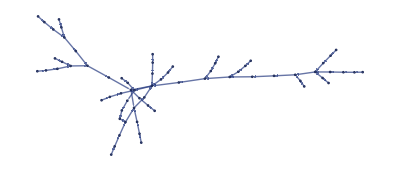

```mathematica
plot[final]
```

## Possible Mutations

Insertion

Add new transformation of simple signature

Add new transformation of random signature

Add new transformation of signature which can apply

Deletion

Remove replacement entirely

Remove one piece of rhs or lhs

Remove one element in a relation

Modification

Swap one full replacement for a random one

Swap one element in a replacement (either side)

Add one element to a replacement (either side)

## Rule Mutation

#### Generation

```mathematica
generateRandomRule[maxRelations_, maxElements_, maxPieces_] := 
	ResourceFunction["RandomWolframModel"][
		generateRandomSignature[maxRelations, maxElements, maxPieces]
	] // List // Flatten
	
generateRandomSignature[maxRelations_, maxElements_, maxPieces_] := 
	Rule @@ Table[
		Table[
			{RandomInteger[{1, maxRelations}], RandomInteger[{1, maxElements}]},
			RandomInteger[{1, maxPieces}]
		], 
		2
	]
	
generateRandomRelation[elementRange_List, nElementsRange_List] := 
	RandomInteger[elementRange, RandomInteger[nElementsRange]]
```

#### Selection

```mathematica
chooseRandomRelation[rule_] :=
	With[{
			replacement = RandomInteger[{1, Length @ rule}],
			side = RandomInteger[{1, 2}],
			relation = RandomInteger[{1, Length @ rule[[replacement, side]]}]
		},
		{replacement, side, relation}
	]
```

#### Insertion

```mathematica
insertTrivialReplacement[rule_] := 
	Append[rule, {{1, 1}} -> {{1, 1}}]
		
insertRandomReplacement[rule_, maxRelations_, maxElements_, maxPieces_] := 
	Append[rule, 
		ResourceFunction["RandomWolframModel"][
			generateRandomSignature[maxRelations, maxElements, maxPieces]
		]
	]
	
insertRandomRelation[rule_, elementRange_List, nElementsRange_List] :=
	With[{relation = chooseRandomRelation[rule]},
		ReplacePart[rule, relation -> Sequence[
			rule[[Sequence @@ relation]], generateRandomRelation[elementRange, nElementsRange]
		]]
	]
	
insertRandomElement[rule_] := Nothing
```

#### Deletion

```mathematica
deleteRandomReplacement[rule_] :=
	Delete[
		rule,
		RandomInteger[{1, Length[rule]}]
	]

deleteRandomRelation[rule_] :=
	Delete[rule, chooseRandomRelation[rule]]
	
deleteRandomElement[rule_] := Nothing
```

#### Replacement

```mathematica
replaceRandomRelation[rule_, elementRange_List, nElementsRange_List] := 
	With[{
			replacement = RandomInteger[{1, Length @ rule}],
			side = RandomInteger[{1, 2}],
			relation = RandomInteger[{1, Length @ rule[[replacement, side]]}]
		},
		ReplacePart[rule, {replacement, side, relation} -> 
			generateRandomRelation[elementRange, nElementsRange]
		]
	]
```

#### Utility

```mathematica
relationSignature[relation_] := 
	List@@Reverse[#] & /@ Normal[Counts[Length /@ relation]]
	
ruleSignature[rule_] :=
	Map[relationSignature[First @ #] -> relationSignature[Last @ #] &, rule]
```

#### Target Function

```mathematica
graphDimension[graph_] := 
	ResourceFunction["WolframHausdorffDimension"][Graph[graph], All, "VertexMethod" -> Max]
```

```mathematica
rule
```

{{{1,2},{2,3}}→{{2,4},{4,1},{1,3}}}

```mathematica
elementRange = {1,5};
nElementsRange = {1,3};
nRules = 3;
```

```mathematica
ruleInsertions =Table[insertRandomRelation[rule, elementRange, nElementsRange], nRules]
```

{{{{1,2},{2,3}}→{{2,4},{4,1},{2,1,3},{1,3}}},{{{1,2},{2,3}}→{{2,4},{4,1},{1,3},{3}}},{{{1,2},{2,3}}→{{2,4},{2,2},{4,1},{1,3}}}}

```mathematica
ruleDeletions = Table[deleteRandomRelation[rule], nRules]
```

{{{{1,2},{2,3}}→{{2,4},{1,3}}},{{{2,3}}→{{2,4},{4,1},{1,3}}},{{{1,2},{2,3}}→{{4,1},{1,3}}}}

```mathematica
ruleReplacements = Table[replaceRandomRelation[rule, elementRange, nElementsRange], nRules]
```

{{{{1,2},{2,3}}→{{2,4},{4},{1,3}}},{{{1,2},{2,3}}→{{3,5,4},{4,1},{1,3}}},{{{1,2},{2,3}}→{{2,4},{5},{1,3}}}}

```mathematica
allRules = Flatten[Join[ruleInsertions,ruleDeletions,ruleReplacements],1];
```

```mathematica
steps=7;
```

```mathematica
GraphicsGrid[Partition[Labeled[Framed[ResourceFunction["WolframModelPlot"][ResourceFunction["WolframModel"][#,Automatic,steps,"FinalState"],ImageSize->140],FrameStyle->LightGray],RulePlot[ResourceFunction["WolframModel"][#],ImageSize->Tiny,"RulePartsAspectRatio"->1]]&/@allRules,3],ImageSize->Full,Alignment->Bottom]
```

-Graphics-

## Dimensionality

```mathematica
PairedDimension[{rule_,init_,steps_}]:=With[{wm=ResourceFunction["WolframModel"][rule,init,steps,"StatesList"]},GraphicsColumn[{ResourceFunction["WolframModelPlot"][Last[wm]],ListLinePlot[Select[Length[#]>3&]@(HypergraphDimensionEstimateList/@(If[Length[#]>20,Take[#,1;;-1;;Floor[Length[#]/20]],#]&@Select[wm,Length[#]>10&])),Frame->True,PlotRange->{0,Automatic},PlotStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["GenericLinePlot","PlotStyles"]]},Frame->True,FrameStyle->LightGray]];
HypergraphDimensionEstimateList[hg_]:=ResourceFunction["LogDifferences"][MeanAround/@Transpose[Values[ResourceFunction["HypergraphNeighborhoodVolumes"][hg,All,Automatic]]]];
GraphicsGrid[Partition[ParallelMap[PairedDimension,{{{{x,y}}->{{x,z},{y,z},{z,z}},{{1,1}},5},{{{x,y}}->{{y,z},{y,w},{z,w},{z,x}},{{0,0}},6},{{{1,2,3}}->{{4,4,2},{4,1,3}},{{0,0,0}},10},{{{1,2},{1,3}}->{{1,4},{1,5},{2,4},{4,3},{5,3}},{{0,0},{0,0}},11},{{{1,2},{3,2}}->{{4,5},{4,1},{5,1},{5,2},{3,4}},{{0,0},{0,0}},11},{{{1,2},{1,3},{4,2}}->{{5,2},{5,2},{5,1},{5,4},{3,5}},{{0,0},{0,0},{0,0}},16},{{{1,2,3},{2,4,5}}->{{4,5,4},{5,6,1},{3,2,6}},{{0,0,0},{0,0,0}},18},{{{1,2},{1,3},{4,2}}->{{5,1},{5,1},{5,3},{5,4},{1,2}},{{0,0},{0,0},{0,0}},16},{{{1,2,3},{2,4,5}}->{{6,7,2},{5,7,8},{4,2,8},{9,3,5}},{{0,0,0},{0,0,0}},18},{{{1,2,3},{1,4,5}}->{{3,2,6},{2,5,6},{7,4,3},{1,8,7}},{{0,0,0},{0,0,0}},19},{{{1,2,3},{3,4}}->{{5,5,5},{5,6,4},{3,1},{1,5}},{{0,0,0},{0,0}},16},{{{1,2,3},{2,4}}->{{5,6,4},{4,1,6},{2,1},{3,6}},{{0,0,0},{0,0}},50}}],4],ImageSize->Full,Alignment->Bottom]
```

-Graphics-

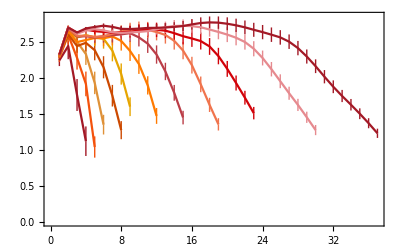

```mathematica
HypergraphDimensionEstimateList[hg_]:=ResourceFunction["LogDifferences"][MeanAround/@Transpose[Values[ResourceFunction["HypergraphNeighborhoodVolumes"][hg,All,Automatic]]]];
ListLinePlot[Select[Length[#]>3&][HypergraphDimensionEstimateList/@Drop[ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{1,2},{1,3}},16,"StatesList"],4]],Frame->True,PlotStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["GenericLinePlot","PlotStyles"]]
```

```mathematica
graph = ResourceFunction["WolframModel"][{{1,2},{3,2}}->{{4,5},{4,1},{5,1},{5,2},{3,4}},{{0,0},{0,0}},11, "FinalState"];
```

```mathematica
ResourceFunction["HypergraphNeighborhoodVolumes"][graph, All, Automatic];
```

```mathematica
HypergraphDimensionEstimateList[hg_]:=ResourceFunction["LogDifferences"][MeanAround/@Transpose[Values[ResourceFunction["HypergraphNeighborhoodVolumes"][hg,All,Automatic]]]];
```

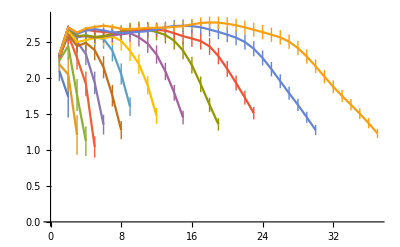

```mathematica
ListLinePlot[HypergraphDimensionEstimateList/@Drop[ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}}, {{1,2},{1,3}},16,"StatesList"],4]]
```

```mathematica
g=final;
```

```mathematica
ResourceFunction["WolframHausdorffDimension"][g, All, "AllDimensions"]
```

[{{36,10},{20,3},{46,8},{32,47},{47,22},{22,15},{33,48},{48,23},{23,1},{34,49},{49,16},{16,14},{14,50},{50,1},{1,5},{35,51},{51,24},{24,5},{7,52},{52,5},{5,36},{10,53},{53,15},{15,11},{37,54},{54,25},{25,17},{38,55},{55,26},{26,18},{12,56},{56,18},{18,8},{39,57},{57,27},{27,19},{40,58},{58,28},{28,20},{41,59},{59,6},{6,3},{29,60},{60,3},{3,9},{42,61},{61,9},{9,13},{13,62},{62,19},{19,14},{43,63},{63,30},{30,1},{44,64},{64,21},{21,11},{11,65},{65,1},{1,4},{45,66},{66,31},{31,4},{2,67},{67,17},{17,46},{8,68},{68,4},{4,11}},All,AllDimensions]

```mathematica
g
```

{{36,10},{20,3},{46,8},{32,47},{47,22},{22,15},{33,48},{48,23},{23,1},{34,49},{49,16},{16,14},{14,50},{50,1},{1,5},{35,51},{51,24},{24,5},{7,52},{52,5},{5,36},{10,53},{53,15},{15,11},{37,54},{54,25},{25,17},{38,55},{55,26},{26,18},{12,56},{56,18},{18,8},{39,57},{57,27},{27,19},{40,58},{58,28},{28,20},{41,59},{59,6},{6,3},{29,60},{60,3},{3,9},{42,61},{61,9},{9,13},{13,62},{62,19},{19,14},{43,63},{63,30},{30,1},{44,64},{64,21},{21,11},{11,65},{65,1},{1,4},{45,66},{66,31},{31,4},{2,67},{67,17},{17,46},{8,68},{68,4},{4,11}}

```mathematica
ResourceFunction["WolframHausdorffDimension"][GridGraph[{20,20}], All, "AllDimensions"]
```

<|1→1.87042,2→1.79377,3→1.75956,4→1.74351,5→1.73659,6→1.73446,7→1.73469,8→1.73585,9→1.73707,10→1.7378,11→1.7378,12→1.73707,13→1.73585,14→1.73469,15→1.73446,16→1.73659,17→1.74351,18→1.75956,19→1.79377,20→1.87042,21→1.79377,22→1.71311,23→1.67686,24→1.6582,25→1.64879,26→1.64448,27→1.64297,28→1.64284,29→1.6432,30→1.64352,31→1.64352,32→1.6432,33→1.64284,34→1.64297,35→1.64448,36→1.64879,37→1.6582,38→1.67686,39→1.71311,40→1.79377,41→1.75956,42→1.67686,43→1.63518,44→1.6148,45→1.60377,46→1.59807,47→1.59543,48→1.59445,49→1.59426,50→1.59431,51→1.59431,52→1.59426,53→1.59445,54→1.59543,55→1.59807,56→1.60377,57→1.6148,58→1.63518,59→2.04238,60→2.18927,61→1.74351,62→1.6582,63→1.6148,64→1.58956,65→1.57728,66→1.57054,67→1.56707,68→1.56548,69→1.56489,70→1.56475,71→1.56475,72→1.56489,73→1.56548,74→1.56707,75→1.57054,76→1.57728,77→1.58956,78→1.87932,79→1.95535,80→2.09814,81→1.73659,82→1.64879,83→1.60377,84→1.57728,85→1.56077,86→1.55316,87→1.54903,88→1.54696,89→1.54606,90→1.54575,91→1.54575,92→1.54606,93→1.54696,94→1.54903,95→1.55316,96→1.56077,97→1.76207,98→1.81585,99→1.8874,100→2.02653,101→1.73446,102→1.64448,103→1.59807,104→1.57054,105→1.55316,106→1.54183,107→1.5371,108→1.53461,109→1.53344,110→1.533,111→1.533,112→1.53344,113→1.53461,114→1.5371,115→1.54183,116→1.67547,117→1.71563,118→1.76577,119→1.83211,120→1.96776,121→1.73469,122→1.64297,123→1.59543,124→1.56707,125→1.54903,126→1.5371,127→1.52901,128→1.52611,129→1.52468,130→1.52412,131→1.52412,132→1.52468,133→1.52611,134→1.52901,135→1.61147,136→1.6421,137→1.67926,138→1.72479,139→1.78532,140→1.91739,141→1.73585,142→1.64284,143→1.59445,144→1.56548,145→1.54696,146→1.53461,147→1.52611,148→1.5201,149→1.51839,150→1.51768,151→1.51768,152→1.51839,153→1.5201,154→1.56528,155→1.58855,156→1.61668,157→1.64988,158→1.68983,159→1.74386,160→1.87206,161→1.73707,162→1.6432,163→1.59426,164→1.56489,165→1.54606,166→1.53344,167→1.52468,168→1.51839,169→1.51374,170→1.51287,171→1.51287,172→1.51374,173→1.53388,174→1.55096,175→1.57214,176→1.59684,177→1.625,178→1.65853,179→1.70518,180→1.82905,181→1.7378,182→1.64352,183→1.59431,184→1.56475,185→1.54575,186→1.533,187→1.52412,188→1.51768,189→1.51287,190→1.50924,191→1.50924,192→1.51544,193→1.52684,194→1.54217,195→1.56036,196→1.5806,197→1.6026,198→1.62887,199→1.66698,200→1.78585,201→1.7378,202→1.64352,203→1.59431,204→1.56475,205→1.54575,206→1.533,207→1.52412,208→1.51768,209→1.51287,210→1.50924,211→1.50924,212→1.51493,213→1.5248,214→1.53745,215→1.55164,216→1.56622,217→1.58105,218→1.59896,219→1.62704,220→1.74002,221→1.73707,222→1.6432,223→1.59426,224→1.56489,225→1.54606,226→1.53344,227→1.52468,228→1.51839,229→1.51374,230→1.51544,231→1.51493,232→1.51917,233→1.52655,234→1.5355,235→1.54451,236→1.55211,237→1.55868,238→1.56677,239→1.58272,240→1.68884,241→1.73585,242→1.64284,243→1.59445,244→1.56548,245→1.54696,246→1.53461,247→1.52611,248→1.5201,249→1.53388,250→1.52684,251→1.5248,252→1.52655,253→1.53034,254→1.53436,255→1.53665,256→1.53584,257→1.53247,258→1.5287,259→1.53057,260→1.6294,261→1.73469,262→1.64297,263→1.59543,264→1.56707,265→1.54903,266→1.5371,267→1.52901,268→1.56528,269→1.55096,270→1.54217,271→1.53745,272→1.5355,273→1.53436,274→1.53181,275→1.52546,276→1.51451,277→1.49969,278→1.48292,279→1.46958,280→1.56056,281→1.73446,282→1.64448,283→1.59807,284→1.57054,285→1.55316,286→1.54183,287→1.61147,288→1.58855,289→1.57214,290→1.56036,291→1.55164,292→1.54451,293→1.53665,294→1.52546,295→1.50892,296→1.48685,297→1.45968,298→1.42884,299→1.39888,300→1.48138,301→1.73659,302→1.64879,303→1.60377,304→1.57728,305→1.56077,306→1.67547,307→1.6421,308→1.61668,309→1.59684,310→1.5806,311→1.56622,312→1.55211,313→1.53584,314→1.51451,315→1.48685,316→1.45267,317→1.41201,318→1.36576,319→1.31745,320→1.39077,321→1.74351,322→1.6582,323→1.6148,324→1.58956,325→1.76207,326→1.71563,327→1.67926,328→1.64988,329→1.625,330→1.6026,331→1.58105,332→1.55868,333→1.53247,334→1.49969,335→1.45968,336→1.41201,337→1.35637,338→1.29298,339→1.22411,340→1.28745,341→1.75956,342→1.67686,343→1.63518,344→1.87932,345→1.81585,346→1.76577,347→1.72479,348→1.68983,349→1.65853,350→1.62887,351→1.59896,352→1.56677,353→1.5287,354→1.48292,355→1.42884,356→1.36576,357→1.29298,358→1.20997,359→1.11751,360→1.17001,361→1.79377,362→1.71311,363→2.04238,364→1.95535,365→1.8874,366→1.83211,367→1.78532,368→1.74386,369→1.70518,370→1.66698,371→1.62704,372→1.58272,373→1.53057,374→1.46958,375→1.39888,376→1.31745,377→1.22411,378→1.11751,379→0.996657,380→1.03764,381→1.87042,382→2.2878,383→2.16455,384→2.07217,385→1.99885,386→1.93786,387→1.88468,388→1.83587,389→1.78855,390→1.74002,391→1.68749,392→1.62776,393→1.5585,394→1.47874,395→1.38723,396→1.28245,397→1.1624,398→1.0245,399→0.865397,400→1.87042|>

```mathematica
g
```

{{36,10},{20,3},{46,8},{32,47},{47,22},{22,15},{33,48},{48,23},{23,1},{34,49},{49,16},{16,14},{14,50},{50,1},{1,5},{35,51},{51,24},{24,5},{7,52},{52,5},{5,36},{10,53},{53,15},{15,11},{37,54},{54,25},{25,17},{38,55},{55,26},{26,18},{12,56},{56,18},{18,8},{39,57},{57,27},{27,19},{40,58},{58,28},{28,20},{41,59},{59,6},{6,3},{29,60},{60,3},{3,9},{42,61},{61,9},{9,13},{13,62},{62,19},{19,14},{43,63},{63,30},{30,1},{44,64},{64,21},{21,11},{11,65},{65,1},{1,4},{45,66},{66,31},{31,4},{2,67},{67,17},{17,46},{8,68},{68,4},{4,11}}

```mathematica
ResourceFunction["WolframHausdorffDimension"][Graph@g, All, "VertexMethod"->#]&/@{Max,Min,Mean}
```

{2.16982,1.22743,1.69652}

```mathematica
ResourceFunction["WolframHausdorffDimension"][GridGraph[{10,10}], All, "VertexMethod"->#]&/@{Max,Min,Mean}
```

{2.05805,1.24891,1.61878}

```mathematica
TripledDimension[{rule_, init_, steps_}] :=
  	With[{wm = ResourceFunction["WolframModel"][rule, init, steps, "StatesList"]},
   		GraphicsColumn[{ResourceFunction["WolframModelPlot"][Last[wm]],
		ListLinePlot[Select[Length[#] > 3 &]@(HypergraphDimensionEstimateList /@ (If[Length[#] > 20, Take[#, 1 ;; -1 ;; Floor[Length[#]/20]], #] &@Select[wm, Length[#] > 10 &])), Frame -> True, PlotRange -> {0, Automatic}, PlotStyle -> ResourceFunction["WolframPhysicsProjectStyleData"]["GenericLinePlot", "PlotStyles"]],

     		Text[(N[ResourceFunction["WolframHausdorffDimension"][ResourceFunction["HypergraphToGraph"][Last[wm]], All, "VertexMethod" -> #], 2])&/@{Min,Mean,Max}]}, Frame -> True, FrameStyle -> LightGray]];
		
HypergraphDimensionEstimateList[hg_] := ResourceFunction["LogDifferences"][MeanAround /@ Transpose[Values[ResourceFunction["HypergraphNeighborhoodVolumes"][hg, All, Automatic]]]];
GraphicsGrid[Partition[ParallelMap[TripledDimension, {{{{x, y}} -> {{x, z}, {y, z}, {z, z}}, {{1, 1}}, 5}, {{{x, y}} -> {{y, z}, {y, w}, {z, w}, {z, x}}, {{0, 0}}, 6}, {{{1, 2, 3}} -> {{4, 4, 2}, {4, 1, 3}}, {{0, 0, 0}}, 10}, {{{1, 2}, {1, 3}} -> {{1, 4}, {1, 5}, {2, 4}, {4, 3}, {5, 3}}, {{0, 0}, {0, 0}}, 11}, {{{1, 2}, {3, 2}} -> {{4, 5}, {4, 1}, {5, 1}, {5, 2}, {3, 4}}, {{0, 0}, {0, 0}}, 11}, {{{1, 2}, {1, 3}, {4, 2}} -> {{5, 2}, {5, 2}, {5, 1}, {5, 4}, {3, 5}}, {{0, 0}, {0, 0}, {0, 0}}, 16}, {{{1, 2, 3}, {2, 4, 5}} -> {{4, 5, 4}, {5, 6, 1}, {3, 2, 6}}, {{0, 0, 0}, {0, 0, 0}}, 18}, {{{1, 2}, {1, 3}, {4, 2}} -> {{5, 1}, {5, 1}, {5, 3}, {5, 4}, {1, 2}}, {{0, 0}, {0, 0}, {0, 0}}, 16}, {{{1, 2, 3}, {2, 4, 5}} -> {{6, 7, 2}, {5, 7, 8}, {4, 2, 8}, {9, 3, 5}}, {{0, 0, 0}, {0, 0, 0}}, 18}, {{{1, 2, 3}, {1, 4, 5}} -> {{3, 2, 6}, {2, 5, 6}, {7, 4, 3}, {1, 8, 7}}, {{0, 0, 0}, {0, 0, 0}}, 19}, {{{1, 2, 3}, {3, 4}} -> {{5, 5, 5}, {5, 6, 4}, {3, 1}, {1, 5}}, {{0, 0, 0}, {0, 0}}, 16}, {{{1, 2, 3}, {2, 4}} -> {{5, 6, 4}, {4, 1, 6}, {2, 1}, {3, 6}}, {{0, 0, 0}, {0, 0}}, 50}}], 4], ImageSize -> Full, Alignment -> Bottom]
```

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

-Graphics-

```mathematica
wm=ResourceFunction["WolframModel"][{{x,y}}->{{x,y},{x,z},{y,z}}, {{0,0}}, 5, "FinalState"]
```

{{0,0},{0,41},{0,41},{0,14},{0,42},{14,42},{0,14},{0,43},{14,43},{0,5},{0,44},{5,44},{0,15},{0,45},{15,45},{5,15},{5,46},{15,46},{0,5},{0,47},{5,47},{0,16},{0,48},{16,48},{5,16},{5,49},{16,49},{0,2},{0,50},{2,50},{0,17},{0,51},{17,51},{2,17},{2,52},{17,52},{0,6},{0,53},{6,53},{0,18},{0,54},{18,54},{6,18},{6,55},{18,55},{2,6},{2,56},{6,56},{2,19},{2,57},{19,57},{6,19},{6,58},{19,58},{0,2},{0,59},{2,59},{0,20},{0,60},{20,60},{2,20},{2,61},{20,61},{0,7},{0,62},{7,62},{0,21},{0,63},{21,63},{7,21},{7,64},{21,64},{2,7},{2,65},{7,65},{2,22},{2,66},{22,66},{7,22},{7,67},{22,67},{0,1},{0,68},{1,68},{0,23},{0,69},{23,69},{1,23},{1,70},{23,70},{0,8},{0,71},{8,71},{0,24},{0,72},{24,72},{8,24},{8,73},{24,73},{1,8},{1,74},{8,74},{1,25},{1,75},{25,75},{8,25},{8,76},{25,76},{0,3},{0,77},{3,77},{0,26},{0,78},{26,78},{3,26},{3,79},{26,79},{0,9},{0,80},{9,80},{0,27},{0,81},{27,81},{9,27},{9,82},{27,82},{3,9},{3,83},{9,83},{3,28},{3,84},{28,84},{9,28},{9,85},{28,85},{1,3},{1,86},{3,86},{1,29},{1,87},{29,87},{3,29},{3,88},{29,88},{1,10},{1,89},{10,89},{1,30},{1,90},{30,90},{10,30},{10,91},{30,91},{3,10},{3,92},{10,92},{3,31},{3,93},{31,93},{10,31},{10,94},{31,94},{0,1},{0,95},{1,95},{0,32},{0,96},{32,96},{1,32},{1,97},{32,97},{0,11},{0,98},{11,98},{0,33},{0,99},{33,99},{11,33},{11,100},{33,100},{1,11},{1,101},{11,101},{1,34},{1,102},{34,102},{11,34},{11,103},{34,103},{0,4},{0,104},{4,104},{0,35},{0,105},{35,105},{4,35},{4,106},{35,106},{0,12},{0,107},{12,107},{0,36},{0,108},{36,108},{12,36},{12,109},{36,109},{4,12},{4,110},{12,110},{4,37},{4,111},{37,111},{12,37},{12,112},{37,112},{1,4},{1,113},{4,113},{1,38},{1,114},{38,114},{4,38},{4,115},{38,115},{1,13},{1,116},{13,116},{1,39},{1,117},{39,117},{13,39},{13,118},{39,118},{4,13},{4,119},{13,119},{4,40},{4,120},{40,120},{13,40},{13,121},{40,121}}

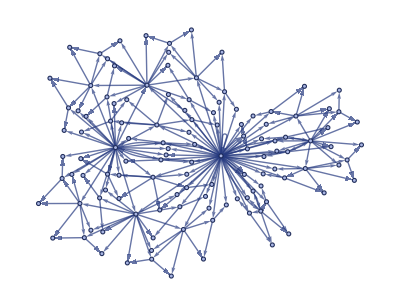

```mathematica
ResourceFunction["WolframModelPlot"][wm]
```

```mathematica
ResourceFunction["WolframHausdorffDimension"][wm, All, "VertexMethod"->Max]
```

[{{0,0},{0,41},{0,41},{0,14},{0,42},{14,42},{0,14},{0,43},{14,43},{0,5},{0,44},{5,44},{0,15},{0,45},{15,45},{5,15},{5,46},{15,46},{0,5},{0,47},{5,47},{0,16},{0,48},{16,48},{5,16},{5,49},{16,49},{0,2},{0,50},{2,50},{0,17},{0,51},{17,51},{2,17},{2,52},{17,52},{0,6},{0,53},{6,53},{0,18},{0,54},{18,54},{6,18},{6,55},{18,55},{2,6},{2,56},{6,56},{2,19},{2,57},{19,57},{6,19},{6,58},{19,58},{0,2},{0,59},{2,59},{0,20},{0,60},{20,60},{2,20},{2,61},{20,61},{0,7},{0,62},{7,62},{0,21},{0,63},{21,63},{7,21},{7,64},{21,64},{2,7},{2,65},{7,65},{2,22},{2,66},{22,66},{7,22},{7,67},{22,67},{0,1},{0,68},{1,68},{0,23},{0,69},{23,69},{1,23},{1,70},{23,70},{0,8},{0,71},{8,71},{0,24},{0,72},{24,72},{8,24},{8,73},{24,73},{1,8},{1,74},{8,74},{1,25},{1,75},{25,75},{8,25},{8,76},{25,76},{0,3},{0,77},{3,77},{0,26},{0,78},{26,78},{3,26},{3,79},{26,79},{0,9},{0,80},{9,80},{0,27},{0,81},{27,81},{9,27},{9,82},{27,82},{3,9},{3,83},{9,83},{3,28},{3,84},{28,84},{9,28},{9,85},{28,85},{1,3},{1,86},{3,86},{1,29},{1,87},{29,87},{3,29},{3,88},{29,88},{1,10},{1,89},{10,89},{1,30},{1,90},{30,90},{10,30},{10,91},{30,91},{3,10},{3,92},{10,92},{3,31},{3,93},{31,93},{10,31},{10,94},{31,94},{0,1},{0,95},{1,95},{0,32},{0,96},{32,96},{1,32},{1,97},{32,97},{0,11},{0,98},{11,98},{0,33},{0,99},{33,99},{11,33},{11,100},{33,100},{1,11},{1,101},{11,101},{1,34},{1,102},{34,102},{11,34},{11,103},{34,103},{0,4},{0,104},{4,104},{0,35},{0,105},{35,105},{4,35},{4,106},{35,106},{0,12},{0,107},{12,107},{0,36},{0,108},{36,108},{12,36},{12,109},{36,109},{4,12},{4,110},{12,110},{4,37},{4,111},{37,111},{12,37},{12,112},{37,112},{1,4},{1,113},{4,113},{1,38},{1,114},{38,114},{4,38},{4,115},{38,115},{1,13},{1,116},{13,116},{1,39},{1,117},{39,117},{13,39},{13,118},{39,118},{4,13},{4,119},{13,119},{4,40},{4,120},{40,120},{13,40},{13,121},{40,121}},All,VertexMethod→Max]

```mathematica
ResourceFunction["HypergraphToGraph"][wm]
```

-Graphics-

```mathematica
ResourceFunction["WolframHausdorffDimension"][ResourceFunction["HypergraphToGraph"][wm], All, "VertexMethod"->Max]
```

2.57518

```mathematica
AgeHypergraphPlot[evolutionObject_,gradientList_:{Red,Blue},exp_:.25]:=With[{totalGenerationsCount=evolutionObject["TotalGenerationsCount"]},ResourceFunction["WolframModelPlot"][evolutionObject[-1],EdgeStyle->Association[MapThread[#1->Directive[Thick,Opacity[.9],Blend[gradientList,1-Exp[exp (#2-totalGenerationsCount)]]]&,{evolutionObject["AllExpressions"],evolutionObject["ExpressionGenerations"]}]],VertexSize->0,VertexStyle->Transparent]];
AgeHypergraphPlot[ResourceFunction["WolframModel"][#,{{0,0,0},{0,0,0}},500],{Hue[1,0.81,0.89],Hue[0.5700000000000001,0.16,0.86],Hue[0.59,0.15,0.89]},.0018]&/@{{{1,2,2},{3,1,4}}->{{2,5,2},{2,3,5},{4,5,5}},{{1,1,2},{1,3,4}}->{{4,4,3},{2,5,3},{2,5,3}},{{1,1,2},{1,3,4}}->{{4,4,5},{5,4,2},{3,2,5}},{{1,2,1},{1,3,4}}->{{4,5,4},{5,4,3},{1,2,5}}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

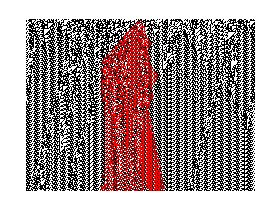
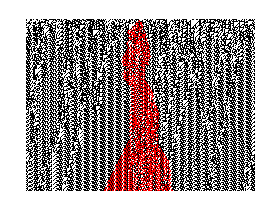

```mathematica
SeedRandom[24246];Table[With[{u=RandomInteger[1,400]},ArrayPlot[Sum[(2+(-1)^i) CellularAutomaton[110,ReplacePart[u,200->i],300],{i,0,1}],ColorRules->{0->White,4->Black,1->Red,3->Red},ImageSize->280]],2]
```

## Replacements based on graph replacements

#### Some weird meta stuff going on

Apply different possible replacements from wolfram models to wolfram model rules

Possibility for recursion

Probably be able to generate the whole universe

Have to choose which paths to go down based on desired behavior